# Comparison of Perturbative and Extracted b dependence

```mathematica
Clear[bmax]
C1 = 1.123;
BB1 = .1669;    (** Gaussian slope from COMPASS for the initial Q.**)
AA = (9/(4 Pi)); (** Parameter for alphaS.  Normalization from 1/beta0 with flavors = 3.***)
LamQCD = .2123; (** Parameter for alphaS.  Lambda_QCD.***)
Q0 = 3.2; (*** Initial Scale of CS evolution. ***)
Qf = 91.0; (** Final Scale of CS evolution.***)
```

```mathematica
bstar[bt_,bmax_] := bt/ Sqrt[1 + bt^2 / bmax^2]  (** Prescription for matching to b_max. **)
mub[bt_,bmax_]:=2*Exp[-EulerGamma]/bstar[bt,bmax]
AlphaS[mu_]:= 1 / (2 AA Log[mu/LamQCD]);
```

```mathematica
gK1[bt_,g2_] :=(g2/2)bt^2
```

Initial and Final Gaussian Fits:

```mathematica
Finit[bt_] := Exp[-2 ((BB1 bt))]
```

Evolution Exponents

```mathematica
evolfactPDF[Q_,bt_,bmax_,g2_] :=(1/AA/ Pi) (Log[Log[Q/LamQCD]/Log[mub[bt,bmax]/LamQCD]] - (4/3) Log[Q/LamQCD](Log[Log[Q/LamQCD]/Log[mub[bt,bmax]/LamQCD]])+ (4/3)Log[Q/mub[bt,bmax]]) - 2 gK1[bt,g2] Log[Q/Q0] 

muintegral[Q_,bt_,bmax_] :=(1/AA/ Pi) (Log[Log[Q/LamQCD]/Log[mub[bt,bmax]/LamQCD]] - (4/3) Log[Q/LamQCD](Log[Log[Q/LamQCD]/Log[mub[bt,bmax]/LamQCD]])+ (4/3)Log[Q/mub[bt,bmax]])  
(** Evolution factor with Gaussian g_K.**)
```

Multiplying Gaussian by the exponential of evolution terms.

```mathematica
fullPDF1[bt_,Q_,bmax_,g2_] := Finit[bt] Exp[evolfactPDF[Q,bt,bmax,g2]]  (**Evolved cross section.**)
fullPDF2[bt_,Q_,bmax_,g2_] := Finit[bt]Exp[muintegral[Q,bt,bmax]]  (**Evolved cross section.**)
```

Checking the evolution parameter.

Plot 3: Plotting the normalized initial and final Gaussians :
	- Including both the original COMPASS fits (Solid) and, 
	- Our refits (Dotted)
Note that everything is normalized to unity in the integration over bT.

This plot should go in the paper.

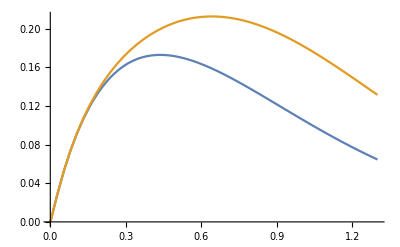

```mathematica
Plot[{bt fullPDF1[bt,Qf,1.5,.2],bt fullPDF1[bt,Qf,0.5,.2]},{bt,.001,1.3}]
```

```mathematica
Integrate[1/x/Log[x],x]
```

Log[Log[x]]